```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
```

```mathematica
Clear[Vp];
μ=50;
nn=49;
wc=μ/(nn+1);
(*Ez=(3/4)*wc;*)
{Ez,me,α,β}={0.5*wc,1,1,0};
data={};
(*x1=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->0.01
x2=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->π*)
For[Vp=0.01,Vp≤π,Vp+=0.05,
{
l=1/Sqrt[me*wc];
kf[n_,sp_]:=Re[Sqrt[2*me*(μ-((n+1/2)*wc-Sign[sp]*Ez/2))]];
(*sn[n_,m_]:=(-1/Pi)*(1/l)*(kf[m,-1]*P1[[n+1,m+1]]-kf[m,+1]*P1[[n+2,m+1]]);*)
sn[n_,m_,sp_]:=(-1/π)*(1/l)*(((β+α)*kf[m,sp]+2*α*kf[m,-sp])*(P1[[n+1,m+1]]-P1[[n+2,m+1]]));
s[n_,sp_]:=Sum[sn[n,m,sp],{m,0,nn+1}];
sm[n_,m_]:=Piecewise[{{s[n,1],n==m&&0≤n≤(nn)},{s[n-(nn+1),-1],n==m&&(nn+1)≤n≤(2*nn+1)}},0];
smatrix=Table[sm[n,m],{n,0,2*nn+1},{m,0,2*nn+1}];
km[n_,m_]:=Piecewise[{{(1/Pi)*(kf[n,+1]-kf[n+1,+1]),n==m&&0≤n≤(nn)},{(1/Pi)*(kf[n-(nn+1),-1]-kf[n+1-(nn+1),-1]),n==m&&(nn+1)≤n≤(2*nn+1)}},0];kmatrix=Table[km[n,m],{n,0,2*nn+1},{m,0,2*nn+1}];
vm[n_,m_]:=Piecewise[{{(1/l)*(β+α)*P2[[n+1,m+1]],0≤n≤(nn)&&0≤m≤(nn)},{(1/l)*2*(α)*P2[[n+1-(nn+1),m+1]],(nn+1)≤n≤(2*nn+1)&&0≤m≤(nn)},{(1/l)*2*(α)*P2[[n+1,m+1-(nn+1)]],0≤n≤(nn)&&(nn+1)≤m≤(2*nn+1)},{(1/l)*(β+α)*P2[[n+1-(nn+1),m+1-(nn+1)]],(nn+1)≤n≤(2*nn+1)&&(nn+1)≤m≤(2*nn+1)}},0];
vmatrix=Table[vm[n,m],{n,0,2*nn+1},{m,0,2*nn+1}];
M=-kmatrix.vmatrix-smatrix;
For[i=0,i≤2*nn+1,i++,
{mm=Eigenvalues[M][[i+1]];
ω=Vp*Re[mm]+(wc);
AppendTo[data,{Vp*me/π,ω/wc}]}];
}]
```

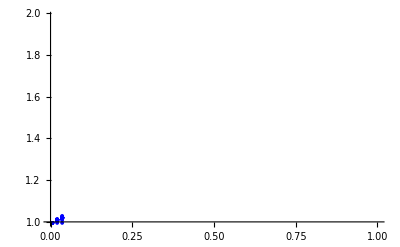

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},Automatic},PlotLegends->SwatchLegend[{Blue},{"ω"}],AxesLabel->{"V_0m_e/π","ω/ω_c"},PlotMarkers->{Automatic,5}]
```

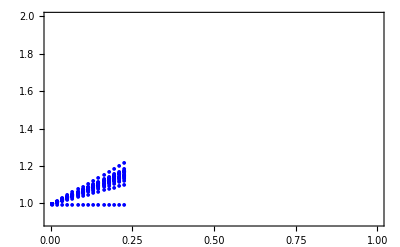

```mathematica
x={0.9,2.0};y=Table[-10+.2*i,{i,0,200}];
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},FrameLabel->{"V_0/π","ω/ω_c",None,None},FrameTicks->{Automatic,y,None,None},PlotMarkers->{Automatic,5},PlotLegends->Placed[Style["(c)",20],{0.15,0.85}]]
```

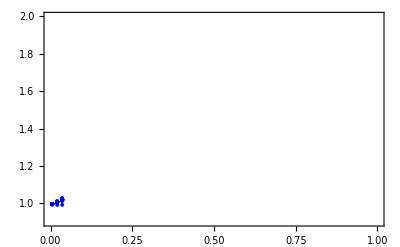

```mathematica
x={0.9,2};y=Table[-10+.2*i,{i,0,200}];
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},FrameStyle->Directive[Thickness[0.006],16],GridLines->{None,None},FrameLabel->{Style["V̄ν",Large],Style["ω/ω_c",Large]},LabelStyle->Directive[12,FontFamily->"Times"],FrameTicks->{Automatic,y,None,None},PlotMarkers->{Automatic,5}]
```

```mathematica
Export["(n+1)(up)&n(up)_Vp=0_Vs=1_Ez=0-5wc_nn=49.eps",Show[f1]];
```

```mathematica
x={0.9,2};y=Table[-10+.2*i,{i,0,200}];
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},FrameLabel->{"V_ρv","ω/ω_c",None,None},FrameTicks->{Automatic,y,None,None},PlotMarkers->{Automatic,5}]
```

-Graphics-

```mathematica
Export["(n+1)(up)&n(up)_Vp=0_Vs=1_Ez=0-5wc_nn=49.png",Show[f1,Frame->{True,True,True,True},FrameLabel->{None,None,None,None},LabelStyle->Directive[Black,20],FrameTicks->{Automatic,y,None,None}],ImageResolution->600,ImageSize->400];
Show[f1]
```

-Graphics-

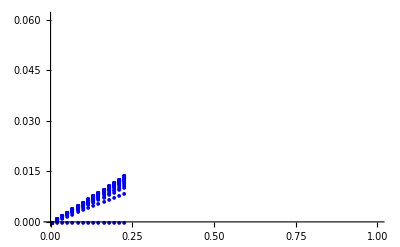

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},Automatic},PlotLegends->SwatchLegend[{Blue},{"ω"}],AxesLabel->{"V_0m_e/π","ω/ω_c"},PlotMarkers->{Automatic,5}]
```

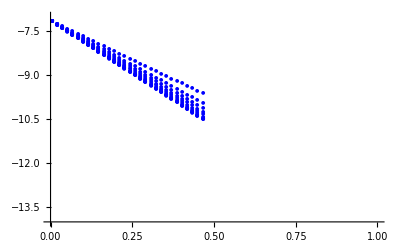

```mathematica
x={-14,-7};
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},PlotLegends->SwatchLegend[{Blue},{"ω"}],AxesLabel->{"V_0m_e/π","ω/ω_c"},PlotMarkers->{Automatic,5}]
```

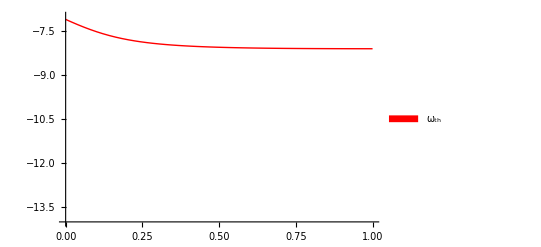

```mathematica
f2=Plot[-(1/wc)*(Ez+Ez*q*(1-α)/(2*(2-(1-α)*q))-Sqrt[Ez^2*((1-α)*q)^2/(4*(2-(1-α)*q)^2)+wc^2*(2-(1-α)*q)/(2-(1+3*α)*q)]),{q,0,1},PlotRange->x,PlotStyle->Red,PlotLegends->SwatchLegend[{Red},{"ω_th"}]]
```

```mathematica
Export["Vs=0_Ez=0-9wc_nn=9.jpg",Show[f1,f2],ImageResolution->600,ImageSize->1000]
```

Vs=0_Ez=0.9wc_nn=9.jpg